# Linear ordinary differential equations

They take the form a_1(x)dy/dx+a_0(x)y=g(x)

In standard form dy/dx+P(x)y=f(x), where P(x)=(a_0(x))/(a_1(x)),a_1(x)≠0

From the standard form we solve the ODE by multiplying by the integrating factor d/dx[ⅇ^(∫P(x)ⅆx)y=ⅇ^(∫P(x)ⅆx)f(x)]

The final solution will be in the form y=y_c+y_p where y_c is the solution associated with the homogeneous DE and y_p is the particular solution of the DE

## Example

Solve dy/dx-3y=0

```mathematica
DSolve[y'[x]-3*y[x]==0,y[x],x]//TraditionalForm
```

{{y(x)→c_1 ⅇ^(3 x)}}

## Using pure functions and Mathematica shorthand

Take a look at the linear ODE dy/dx-3y=0,y(0)=2

If we use DSolve[] and only the argument y instead of y[x] Mathematica returns a pure function

```mathematica
Subscript[ϕ, y0_]=DSolveValue[{y'[x]-3*y[x]==0,y[0]==2},y,x] (* could also use ϕ[yo_]:= *)
```

Function[{x},2 ⅇ^(3 x)]

Since we stored it as a computer variable ϕ_y0, we can solve it for values of x (in a variety of ways)

```mathematica
Subscript[ϕ, y0][3]
```

2 ⅇ^9

```mathematica
Subscript[ϕ, y0]@3
```

2 ⅇ^9

```mathematica
3//Subscript[ϕ, y0]
```

2 ⅇ^9

Because it is a pure function, we have to plot it as follows

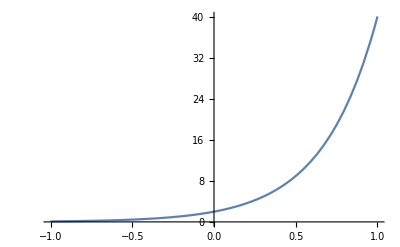

```mathematica
Plot[Subscript[ϕ, y0][x],{x,-1,1}]
```

Using Dsolve[] returns a solution

If we want to evaluate is for values of x we can do it as follows

```mathematica
Subscript[ϕ, y0_]=DSolve[{y'[x]-3*y[x]==0,y[0]==2},y[x],x]
```

{{y[x]→2 ⅇ^(3 x)}}

```mathematica
Subscript[ϕ, y0]/.x->3
```

{{y[3]→2 ⅇ^9}}

Using DSolveValue[...y[x]...] we can plot directly

```mathematica
Subscript[ϕ, y0_]=DSolveValue[{y'[x]-3*y[x]==0,y[0]==2},y[x],x]
```

2 ⅇ^(3 x)

```mathematica
Plot[Subscript[ϕ, y0],{x,-1,1}]
```

-Graphics-

## More examples

Solve dy/dx-3y=6

Note that P(x)=-3 x^0 and f(x)=6 x^0, so that the interval over which this equation holds is (-∞,∞)

```mathematica
(*The constant solution*)
DSolve[y'[x]-3*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]}}

```mathematica
(*The particular solution*)
(*Note how it incorporates the constant solution above*)
DSolve[y'[x]-3*y[x]==6,y[x],x]
```

{{y[x]→-2+ⅇ^(3 x) C[1]}}

```mathematica
Manipulate[Plot[-2+k*ⅇ^(3x),{x,-1,1}],{k,0,2}]
```

Solve dy/dx+y=x,y(0)=4

```mathematica
DSolve[{y'[x]+y[x]==x,y[0]==4},y[x],x]//TraditionalForm
```

{{y(x)→ⅇ^-x (ⅇ^x x-ⅇ^x+5)}}

## YouTube examples

```mathematica
Hyperlink["https://www.youtube.com/watch?v=9gIKA15CYNo&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ&index=12"]
```

Solve dy/dx+y=x, y(0)=4

```mathematica
(*Constant*)
DSolve[{y'[x]+y[x]==0,y[0]==4},y[x],x]
```

{{y[x]→4 ⅇ^-x}}

```mathematica
(*Particular*)
DSolve[{y'[x]+y[x]==x,y[0]==4},y[x],x]//Simplify
```

{{y[x]→-1+5 ⅇ^-x+x}}

The final solution is y(x)=-1+x+9 ⅇ^-x

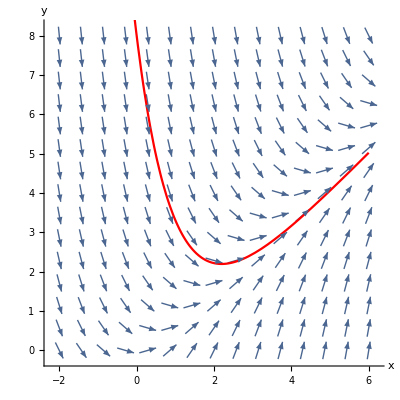

```mathematica
Show[VectorPlot[{1,x-y},{x,-2,6},{y,0,8},VectorScale->{0.04,0.04,None}],Plot[-1+9 ⅇ^-x+x,{x,-2,6},PlotStyle->Red],Frame->None,Axes->True,AxesLabel->{"x","y"}]
```

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π Erf[x]

```mathematica
Erf[x]//TraditionalForm
```

erf(x)

```mathematica
Hyperlink["https://www.youtube.com/watch?v=OZFN1lz8678&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ&index=15"]
```

Solve dy/dx-2xy=2, y(0)=1

```mathematica
DSolve[{y'[x]-2*x*y[x]==0,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(x^2)}}

```mathematica
DSolve[{y'[x]==2+2*x*y[x],y[0]==1},y[x],x]//Simplify
```

{{y[x]→ⅇ^(x^2) (1+√π Erf[x])}}

Solve dT/dt∝100-T

```mathematica
Hyperlink["https://www.youtube.com/watch?v=nPkLYkZDBgo&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ&index=16"]
```

```mathematica
DSolve[T'[t]==-k*T[t]+100*k,T[t],t]
```

{{T[t]→100+ⅇ^(-k t) C[1]}}